```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];

Import["model/data.wl"];
Import["model/plot-utils.wl"];
Import["model/model.wl"];
```

```mathematica
state="CA";

params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
icuCapacity=params["icuBeds"]/params["population"];
thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
hospitalCapacity=(1-params["bedUtilization"])params["staffedBeds"]/params["population"];
hospitalizationData = stateHospitalizationData[state];
```

```mathematica
distance[t_] := stateDistancing[state,scenario1,t];
sol=CovidModelFit[
daysUntilNotInfectiousOrHospitalized0,
daysFromInfectedToInfectious0,
daysUntilNotInfectiousOrHospitalized0,
daysToLeaveHosptialNonCritical0,
pPCRNH0,
pPCRH0,
daysTogoToCriticalCare0,
daysFromCriticalToRecoveredOrDeceased0,
fractionOfCriticalDeceased0,
importlength0,initialInfectionImpulse0,
tmax,
params["pS"],
params["pH"],
params["pC"],
distance,
icuCapacity
]
model[r0natural_,importtime_][i_,t_]:=Through[sol[r0natural,importtime][t],List][[i]]/;And@@NumericQ/@{r0natural,importtime,i,t}
```

ParametricFunction[<>]

```mathematica
longData=Select[Join[{1,#["day"],If[TrueQ[#["deathIncrease"]==Null],0,(#["deathIncrease"]/params["population"])//N]}&/@thisStateData,
{2,#["day"],(#["positiveIncrease"]/params["population"])//N}&/@thisStateData
],#[[3]]>0&];
```

{{1,90.,5.13046×10^-7},{1,89.,2.56523×10^-7},{1,88.,5.64351×10^-7},{1,87.,5.90003×10^-7},{1,86.,3.3348×10^-7},{1,85.,3.07828×10^-7},{1,84.,3.3348×10^-7},{1,83.,3.3348×10^-7},{1,81.,7.69569×10^-8},{1,80.,1.02609×10^-7},{1,79.,5.13046×10^-8},{1,78.,1.28262×10^-7},{1,77.,5.13046×10^-8},{1,76.,1.28262×10^-7},{1,75.,2.56523×10^-8},{1,73.,2.56523×10^-8},{1,71.,1.02609×10^-7},{2,90.,0.0000265501},{2,89.,0.0000189571},{2,88.,0.0000273197},{2,87.,0.0000195984},{2,86.,0.0000223945},{2,85.,0.0000166997},{2,84.,6.49003×10^-6},{2,83.,9.4657×10^-6},{2,82.,5.0535×10^-6},{2,81.,6.59264×10^-6},{2,80.,5.5409×10^-6},{2,79.,3.56567×10^-6},{2,78.,8.02917×10^-6},{2,77.,3.2835×10^-6},{2,76.,3.79654×10^-6},{2,75.,1.0774×10^-6},{2,74.,1.05174×10^-6},{2,73.,1.28262×10^-6},{2,71.,1.15435×10^-6},{2,70.,6.15655×10^-7},{2,69.,4.87394×10^-7},{2,68.,6.6696×10^-7},{2,67.,4.87394×10^-7},{2,66.,2.30871×10^-7},{2,65.,1.79566×10^-7}}

{0.0455,0.091,0.0413636,0.0395652,0.07,0.0758333,0.07,0.07,0.303333,0.2275,0.455,0.182,0.455,0.182,0.91,0.91,0.2275,0.000800097,0.00112057,0.000777559,0.0010839,0.000948568,0.00127204,0.00327312,0.00224417,0.00420355,0.00322218,0.0038338,0.00595755,0.00264569,0.00646953,0.00559527,0.0197167,0.0201976,0.016562,0.0184022,0.0345042,0.0435842,0.03185,0.0435842,0.0920111,0.1183}

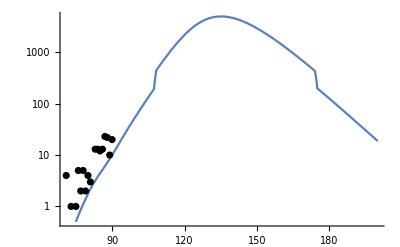

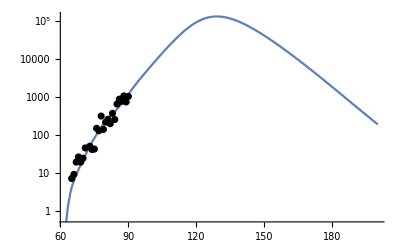

```mathematica
dataWeights=(.91^#[[1]](params["population"]#[[3]])^-1)&/@longData
fit=NonlinearModelFit[
longData,
model[r0natural,importtime][i,t] - model[r0natural,importtime][i,t-1],
{{r0natural, Log[r0natural0]}, {importtime, Log[params["importtime0"]]}},
{i,t},
Weights -> dataWeights,
AccuracyGoal->5,
PrecisionGoal->10
];
Show[
LogPlot[{params["population"]fit[1,t]},{t,60,200},PlotRange->{Automatic,{.5,All}}],
ListLogPlot[{
{#["day"],#["deathIncrease"]}&/@thisStateData
},PlotStyle->Black]
]
Show[
LogPlot[{params["population"]fit[2,t]},{t,60,200},PlotRange->{Automatic,{.5,All}}],
ListLogPlot[{
{#["day"],#["positiveIncrease"]}&/@thisStateData
},PlotStyle->Black]
]
```

```mathematica
ApplylongData[[All,1]]==1
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}==1

```mathematica
longDataIndices1=(#[[1]]==1)&/@longData;
longDataIndices2=(#[[1]]==2)&/@longData;
Grid[{
{"RMS rel. error",
Mean[(fit["FitResiduals"]/longData[[All,3]])^2]^.5},
{"RMS rel. error (deaths inc.)",
Mean[Pick[fit["FitResiduals"]/longData[[All,3]],longDataIndices1]^2]^.5},
{"RMS rel. error (PCR inc.)",
Mean[Pick[fit["FitResiduals"]/longData[[All,3]],longDataIndices2]^2]^.5},
{"Sys. rel. error (deaths inc.)",
Mean[Pick[fit["FitResiduals"]/longData[[All,3]],longDataIndices1]]},
{"Sys. rel. error (PCR inc.)",
Mean[Pick[fit["FitResiduals"]/longData[[All,3]],longDataIndices2]]},
{"R^2(death inc.)",
(Total[#^2])&[Pick[fit["FitResiduals"],longDataIndices1]]/(Total[(#-Mean[#])^2])&[Pick[fit["Response"],longDataIndices1]]},
{"R^2(PCR inc.)",
(Total[#^2])&[Pick[fit["FitResiduals"],longDataIndices2]]/(Total[(#-Mean[#])^2])&[Pick[fit["Response"],longDataIndices2]]}
}]
```

RMS rel. error | 0.507573
RMS rel. error (deaths inc.) | 0.63943
RMS rel. error (PCR inc.) | 0.39343
Sys. rel. error (deaths inc.) | 0.605468
Sys. rel. error (PCR inc.) | 0.0210459
R^2(death inc.) | 1.09282
R^2(PCR inc.) | 0.124271

```mathematica
Length[mask1]
(*RmsRelativeError[fit["FitResiduals"],longData,mask1]*)
Pick[fit["FitResiduals"],mask1]
```

42

{2.57158×10^-7,4.12897×10^-8,3.8221×10^-7,4.34981×10^-7,2.01025×10^-7,1.94596×10^-7,2.37061×10^-7,2.52109×10^-7,2.13871×10^-8,5.7691×10^-8,1.54331×10^-8,9.99076×10^-8,2.91097×10^-8,1.11075×10^-7,1.25129×10^-8,1.82612×10^-8,9.86539×10^-8}

```mathematica
mask1=(#[[1]]==1)&/@longData;
mask2=(#[[1]]==2)&/@longData;
Grid[{
{"RMS rel. error",
RmsRelativeError[fit["FitResiduals"],longData]},
{"RMS rel. error (deaths inc.)",
RmsRelativeError[fit["FitResiduals"],longData,mask1]},
{"RMS rel. error (PCR inc.)",
RmsRelativeError[fit["FitResiduals"],longData,mask2]},
{"Mean. rel. error (deaths inc.)",
MeanRelativeError[fit["FitResiduals"],longData,mask1]},
{"Sys. rel. error (PCR inc.)",
MeanRelativeError[fit["FitResiduals"],longData,mask2]},
{"χ^2 (arbitrary units)",
ChiSquared[fit["FitResiduals"],longData]},
{"R^2(death inc.)",
RSquared[fit["FitResiduals"],longData,mask1]},
{"R^2(PCR inc.)",
RSquared[fit["FitResiduals"],longData,mask2]}}]
```

RMS rel. error | 0.507573
RMS rel. error (deaths inc.) | 0.63943
RMS rel. error (PCR inc.) | 0.39343
Mean. rel. error (deaths inc.) | 0.605468
Sys. rel. error (PCR inc.) | 0.0210459
χ^2 (arbitrary units) | 4.54668×10^-7
R^2(death inc.) | 1.09282
R^2(PCR inc.) | 0.124271

```mathematica
<|"key"->0|>["key"]
```

0